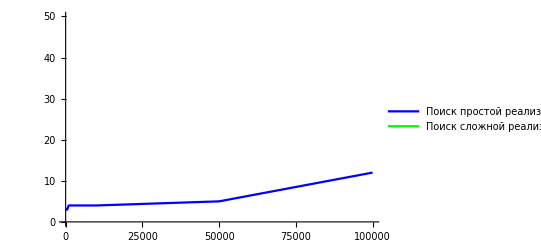

```mathematica
naiveHashSearch= ListLinePlot[{{100, 3}, {500, 3}, {1000, 4}, {5000,4}, {10000, 4}, {50000, 5}, {100000, 12}}, ColorFunction->Function[{}, Blue], PlotLegends->LineLegend[{Blue,Green,Blue, Magenta},{"Поиск простой реализацией","Поиск сложной реализацией"}], PlotRange->{{0, 100000}, {0, 50}}]
```

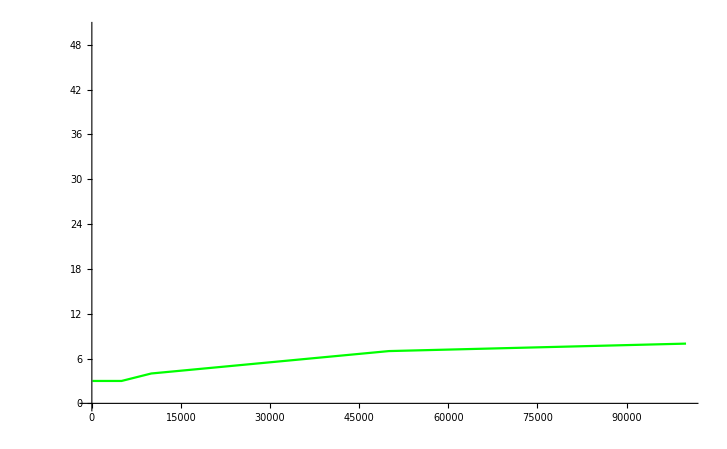

```mathematica
complicatedHashSearch= ListLinePlot[{{100,3}, {500, 3}, {1000, 3}, {5000, 3}, {10000, 4}, {50000, 7}, {100000, 8}}, ColorFunction->Function[{}, Green],  PlotRange->{{0, 100000}, {0, 50}}]
```

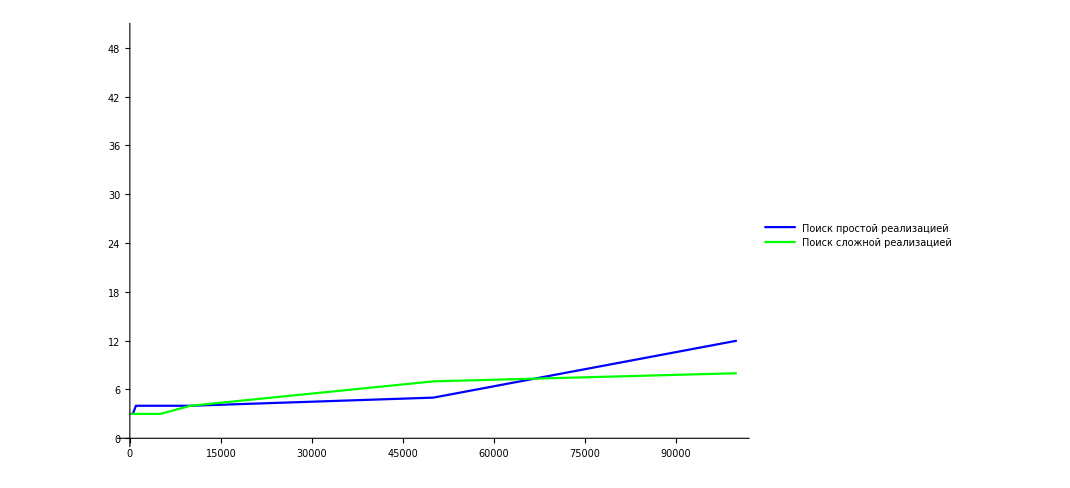

```mathematica
Show[naiveHashSearch, complicatedHashSearch]
```

```mathematica
naiveHashCollisions= ListLinePlot[{{100, 0}, {500, 6}, {1000, 29}, {5000, 735}, {10000, 2345}, {50000, 30928}, {100000, 75298}}, ColorFunction->Function[{}, Black], PlotLegends->LineLegend[{Black, Red},{"Коллизии в простой реализации","Коллизии в сложной реализации"}], PlotRange->{{0, 100000}, {0, 30000}}]
```

-Graphics-

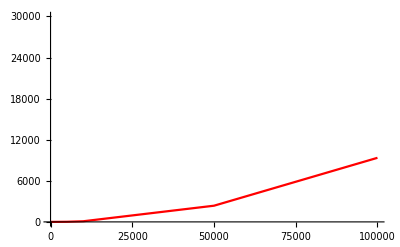

```mathematica
complicatedHashCollisions= ListLinePlot[{{100, 0}, {500, 1}, {1000, 1}, {5000, 16}, {10000, 93}, {50000, 2364}, {100000, 9359}}, ColorFunction->Function[{}, Red], PlotRange->{{0, 100000}, {0, 30000}}]
```

```mathematica
Show[naiveHashCollisions, complicatedHashCollisions]
```

-Graphics-